```mathematica
Quit
```

## Functions

```mathematica
MExp[M_,order_]:= Module[{ans,i,toadd},
ans=toadd=IdentityMatrix[Length[M]];
For[i=1,i≤ order,i++,
toadd=toadd.M/i;
ans=ans+toadd;
];
Return[ans];
]
```

```mathematica
MakeH0[L_,w_]:= 
Table[
Piecewise[{{-w,i==j+1 || j==i+1}},0],
{i,1,L},{j,1,L}
];
```

```mathematica
Diagonalize[M_]:= Module[{λ,U},
{λ,U}=Eigensystem[M];
U=Transpose[Map[Normalize,U]];
Return[{λ,U}];
]
```

```mathematica
CutH0[L_,w_,β_,μ_,cut_]:= Module[{H0,λ,U},
H0=MakeH0[L,w];
{λ,U}=Diagonalize[H0];
λ=Clip[λ,{μ-1/β Log[cut],μ+1/β Log[cut]}];
Return[U.DiagonalMatrix[λ].ConjugateTranspose[U]];
];
```

```mathematica
Makeρ0[L_,w_,β_,μ_,cut_]:= Exp[β μ]MExp[-β (CutH0[L,w,β,μ,cut]),20]
```

```mathematica
MakeH[NL_,NC_,NR_,w_,ww_]:= Module[{ans},
ans=ArrayFlatten[{{MakeH0[NL,w],0,0},{0,MakeH0[NC,w],0},{0,0,MakeH0[NR,w]}}];
ans[[NL+1,NL]]=ans[[NL,NL+1]]= -ww;
ans[[NL+NC+1,NL+NC]]=ans[[NL+NC,NL+NC+1]]= -ww;
Return[ans];
]
```

```mathematica
MakeU[NL_,NC_,NR_]:= ArrayFlatten[{{IdentityMatrix[NL],0,0},{0,ConstantArray[0,{NC,NC}],0},{0,0,IdentityMatrix[NR]}}]
MakeV[NL_,NC_,NR_,w_,βL_,βR_,μL_,μR_,cut_]:= ArrayFlatten[{{Makeρ0[NL,w,βL,μL,cut],0,0},{0,ConstantArray[0,{NC,NC}],0},{0,0,Makeρ0[NR,w,βR,μR,cut]}}]
```

```mathematica
MakeRHS[G_,H_,U_,V_]:= ⅈ(H.G-G.H)-1/2(U.G+G.U)+1/2(V.(IdentityMatrix[Length[G]]-G)+(IdentityMatrix[Length[G]]-G).V);
MakeRHS2[G_,H_,U_,V_]:= ⅈ(H.G-G.H)-1/2(U.G+G.U)-1/2(V.G+G.V);
```

```mathematica
PropagateDt[G_,dt_,H_,U_,V_]:=Module[{order,ans,toadd,i},
order=10;
ans=G;
toadd = MakeRHS[G,H,U,V]*dt;
(*Print[Norm[toadd]];*)
ans+= toadd;
(*Print[Norm[ans]];*)

For[i=2,i≤ order, i++,
toadd=MakeRHS2[toadd,H,U,V]*dt/i;
ans+= toadd;
(*Print[Norm[ans]];*)
(*Print[toadd];
Print["taylor series order number ",i];*)
];
(*Print["Exiting PropagateDt function"];*)
Return[ans];
]
```

```mathematica
GInit[L_,w_,β_,μ_,cut_]:= Inverse[IdentityMatrix[L]+Makeρ0[L,w,β,μ,cut]];

Solver[NL_,NC_,NR_,βL_,βC_,βR_,μL_,μC_,μR_,w_,ww_,t_,dt_,cut_]:=Module[{H,U,V,G,i},
H= MakeH[NL,NC,NR,w,ww];
U= MakeU[NL,NC,NR];
V=MakeV[NL,NC,NR,w,βL,βR,μL,μR,cut];
(*Print[V];*)


G=ArrayFlatten[{{GInit[NL,w,βL,μL,cut],0,0},{0,GInit[NC,w,βC,μC,cut],0},{0,0,GInit[NR,w,βR,μR,cut]}}];
(*Print[Norm[G]];*)
(*Print[G]*)

For[i=1,i≤ Floor[t/dt],i++,
(*If[Mod[i,1000]==0,Print[i]];*)
G=PropagateDt[G,dt,H,U,V];
(*Print[Norm[G]];*)
];

Return[G];
];
```

## Linear Response σ(β) for β ∈ (0.01,0.1) finished on 2015-06-14

```mathematica
NL=5;
NC=9;
NR=5;
NT=NL+NC+NR;

w=1;
ww= 3;

t=100.0;
dt=0.01;

cut=10^2;

μC=0.0;
μL=-0.01;
μR=+0.01;
β=0.1;
```

```mathematica
βL = βC = βR = β;
data = {};

For[i=1, i≤ 19, i++,
G = Solver[NL,NC,NR,βL,βC,βR,μL,μC,μR,w,ww,t,dt,cut];
corrMatrixBC = {{G[[i,i]], G[[i,10]]}, {G[[10,i]], G[[10,10]]}};
SBC = Re[N[-Tr[corrMatrixBC*MatrixLog[corrMatrixBC]+(IdentityMatrix[2]-corrMatrixBC)*MatrixLog[(IdentityMatrix[2]-corrMatrixBC)]]]];
corrMatrixB = G[[10, 10]];
SB = Re[N[-(corrMatrixB*Log[corrMatrixB] + (1-corrMatrixB)*Log[(1-corrMatrixB)])]];
corrMatrixC = G[[i, i]];
SC = Re[N[-(corrMatrixC*Log[corrMatrixC] + (1-corrMatrixC)*Log[(1-corrMatrixC)])]];
MI = N[SB+SC-SBC];
Print[MI];
data=Append[data,MI];
]
```

-1.3863-1. Re[Tr[-0.693147-4.08553×10^-23 ⅈ]]-1. Re[Tr[-0.693147-1.30822×10^-24 ⅈ]]

-1.3863-1. Re[Tr[-0.693147-4.08553×10^-23 ⅈ]]-1. Re[Tr[-0.693147-3.8015×10^-23 ⅈ]]

-1.3863-1. Re[Tr[-0.693147+3.44255×10^-25 ⅈ]]-1. Re[Tr[-0.693147-4.08553×10^-23 ⅈ]]

$Aborted

```mathematica
N[data]
```

{(-1.3863-8.67344×10^-18 ⅈ)-1. Tr[-0.693147-4.08553×10^-23 ⅈ]-1. Tr[-0.693147-1.30822×10^-24 ⅈ],(-1.3863-1.7352×10^-18 ⅈ)-1. Tr[-0.693147-4.08553×10^-23 ⅈ]-1. Tr[-0.693147-3.8015×10^-23 ⅈ],(-1.3863-2.51237×10^-22 ⅈ)-1. Tr[-0.693147+3.44255×10^-25 ⅈ]-1. Tr[-0.693147-4.08553×10^-23 ⅈ],(-1.38629-1.11449×10^-16 ⅈ)-1. Tr[-0.693147-4.08553×10^-23 ⅈ]-1. Tr[-0.693147-5.64208×10^-22 ⅈ],(-1.38629+9.71642×10^-19 ⅈ)-1. Tr[-0.693147-4.08553×10^-23 ⅈ]-1. Tr[-0.693147-4.12046×10^-21 ⅈ],(-1.38629+1.38813×10^-17 ⅈ)-1. Tr[-0.693147-4.08553×10^-23 ⅈ]-1. Tr[-0.693147+1.4813×10^-21 ⅈ],(-1.3863-8.6746×10^-19 ⅈ)-1. Tr[-0.693147-2.68773×10^-22 ⅈ]-1. Tr[-0.693147-4.08553×10^-23 ⅈ],(-1.38629+4.1627×10^-17 ⅈ)-1. Tr[-0.693147-4.08553×10^-23 ⅈ]-1. Tr[-0.693147-1.53715×10^-22 ⅈ],(-1.38664+3.2551×10^-19 ⅈ)-1. Tr[-0.693147+5.39402×10^-22 ⅈ]-1. Tr[-0.693147-4.08553×10^-23 ⅈ],(-4.42687-9.97448×10^-16 ⅈ)+(0.999857+2.85646×10^-19 ⅈ) MatrixLog[{{0.499928+1.42823×10^-19 ⅈ,0.499928+1.42823×10^-19 ⅈ},{0.499928+1.42823×10^-19 ⅈ,0.499928+1.42823×10^-19 ⅈ}}]-2. Tr[-0.693147-4.08553×10^-23 ⅈ],(-1.38664+6.39338×10^-19 ⅈ)-1. Tr[-0.693147+4.91968×10^-22 ⅈ]-1. Tr[-0.693147-4.08553×10^-23 ⅈ],(-1.38629+3.81585×10^-17 ⅈ)-1. Tr[-0.693147-4.08553×10^-23 ⅈ]-1. Tr[-0.693147-3.7964×10^-21 ⅈ],(-1.3863+5.43123×10^-20 ⅈ)-1. Tr[-0.693147+3.92663×10^-22 ⅈ]-1. Tr[-0.693147-4.08553×10^-23 ⅈ],(-1.38629-5.5289×10^-17 ⅈ)-1. Tr[-0.693147-4.08553×10^-23 ⅈ]-1. Tr[-0.693146-2.6686×10^-21 ⅈ],(-1.38629-2.85948×10^-21 ⅈ)-1. Tr[-0.693147-4.08553×10^-23 ⅈ]-1. Tr[-0.693146-2.63488×10^-21 ⅈ],(-1.38629-3.18702×10^-21 ⅈ)-1. Tr[-0.693147-4.08553×10^-23 ⅈ]-1. Tr[-0.693145-3.1128×10^-21 ⅈ],(-1.3863-8.67083×10^-18 ⅈ)-1. Tr[-0.693147-4.08553×10^-23 ⅈ]-1. Tr[-0.693147+2.02666×10^-21 ⅈ],(-1.3863-5.55036×10^-17 ⅈ)-1. Tr[-0.693147-4.08553×10^-23 ⅈ]-1. Tr[-0.693147+4.26359×10^-23 ⅈ],(-1.3863-4.3357×10^-18 ⅈ)-1. Tr[-0.693147-4.08553×10^-23 ⅈ]-1. Tr[-0.693147+1.23672×10^-24 ⅈ]}

```mathematica
SigmavsBeta={};

For[i=1,i≤ 10,i++,
β=0.01*i;
data={};

For[j=1,j≤ 5,j++,

μL=-0.01*j;
μR=+0.01*j;
βL = βC = βR = β;

G=Solver[NL,NC,NR,βL,βC,βR,μL,μC,μR,w,ww,t,dt,cut];
data=Append[data,{μR-μL,Im[G[[NL+NC/2+1,NL+NC/2]]-G[[NL+NC/2,NL+NC/2+1]]]}];
Print[data[[j]]];
];
sigma=LinearModelFit[data,x,x]//Normal//Coefficient[#,x]&;
SigmavsBeta = Append[SigmavsBeta,{β,sigma}];
]
```

{0.02,0.0000265626}

{0.04,0.0000531251}

{0.06,0.0000796877}

{0.08,0.00010625}

{0.1,0.000132812}

{0.02,0.0000311005}

{0.04,0.0000622009}

{0.06,0.0000933011}

{0.08,0.000124401}

{0.1,0.000155501}

{0.02,0.0000334858}

{0.04,0.0000669714}

{0.06,0.000100456}

{0.08,0.000133941}

{0.1,0.000167424}

{0.02,0.0000283623}

{0.04,0.0000567242}

{0.06,0.0000850851}

{0.08,0.000113445}

{0.1,0.000141802}

{0.02,0.0000119848}

{0.04,0.0000239694}

{0.06,0.0000359534}

{0.08,0.0000479368}

{0.1,0.0000599192}

{0.02,-0.0000122601}

{0.04,-0.0000245188}

{0.06,-0.0000367745}

{0.08,-0.000049026}

{0.1,-0.0000612718}

{0.02,3.20249×10^-9}

{0.04,6.40932×10^-9}

{0.06,9.62483×10^-9}

{0.08,1.28534×10^-8}

{0.1,1.60993×10^-8}

{0.02,3.66025×10^-9}

{0.04,7.32696×10^-9}

{0.06,1.10066×10^-8}

{0.08,1.47058×10^-8}

{0.1,1.84309×10^-8}

{0.02,4.1181×10^-9}

{0.04,8.24541×10^-9}

{0.06,1.23912×10^-8}

{0.08,1.65646×10^-8}

{0.1,2.07752×10^-8}

{0.02,4.57606×10^-9}

{0.04,9.16477×10^-9}

{0.06,1.37788×10^-8}

{0.08,1.84309×10^-8}

{0.1,2.31338×10^-8}

$Aborted

```mathematica
SigmavsBeta
```

{{0.1,0.00132812},{0.2,0.001555},{0.3,0.00167423},{0.4,0.001418},{0.5,0.000599181},{0.6,-0.000612653},{0.7,1.61188×10^-7},{0.8,1.846×10^-7},{0.9,2.08167×10^-7},{1.,2.31908×10^-7}}

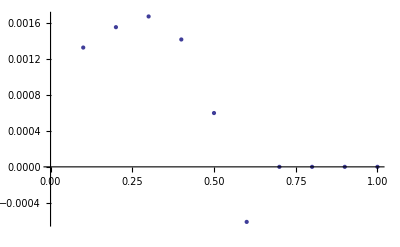

```mathematica
ListPlot[SigmavsBeta]
```

## Linear Response κ for β ∈ (0.01,0.1) finished on 2015-06-15

```mathematica
NL=5;
NC=20;
NR=5;
NT=NL+NC+NR;

μL = μR = μC=0.1;

w=1.0;
ww=1.0;

t=500.0;
dt=0.1;

cut=10^2;
```

```mathematica
βC = 0.01;
βL=βC-0.005;
βR=βC+0.005;
G=Solver[NL,NC,NR,βL,βC,βR,μL,μC,μR,w,ww,t,dt,cut];
```

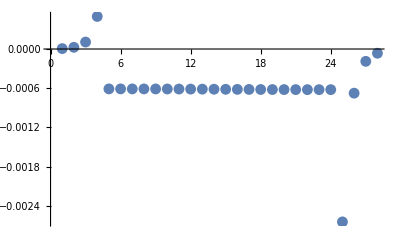

```mathematica
Table[Im[G[[i,i+2]]-G[[i+2,i]]],{i,1,Length[G]-2}]//ListPlot[#,PlotRange->All]&
```

```mathematica
KappavsBeta={};

For[i=1,i≤ 10,i++,
β=0.01*i;
data={};
Print["β = ",β];

For[j=1,j≤ 5,j++,

βC = β;
βR=β(1+0.05j);
βL=β(1-0.05j);

G=Solver[NL,NC,NR,βL,βC,βR,μL,μC,μR,w,ww,t,dt,cut];

data=Append[data,{βR-βL,Im[G[[NL+NC/2+2,NL+NC/2]]-G[[NL+NC/2,NL+NC/2+2]]]}];
Print[data[[j]]];
];
kappa=LinearModelFit[data,x,x]//Normal//Coefficient[#,x]&;
Print["κ=",kappa];
KappavsBeta = Append[KappavsBeta,{β,kappa}];
]
```

β = 0.01

{0.001,0.000062201}

{0.002,0.00012386}

{0.003,0.000185519}

{0.004,0.000247178}

{0.005,0.000308837}

κ=0.0616589

β = 0.02

{0.002,0.000124222}

{0.004,0.000247359}

{0.006,0.000370495}

{0.008,0.000493631}

{0.01,0.000616765}

κ=0.0615679

β = 0.03

{0.003,0.000186027}

{0.006,0.000370425}

{0.009,0.000554822}

{0.012,0.000739214}

{0.015,0.000923603}

κ=0.0614647

β = 0.04

{0.004,0.000247581}

{0.008,0.000492988}

{0.012,0.000738391}

{0.016,0.000983785}

{0.02,0.00122917}

κ=0.0613493

β = 0.05

{0.005,0.000308849}

{0.01,0.000614978}

{0.015,0.000921097}

{0.02,0.0012272}

{0.025,0.00153328}

κ=0.0612219

β = 0.06

{0.006,0.000369796}

{0.012,0.000736325}

{0.018,0.00110284}

{0.024,0.00146932}

{0.03,0.00183577}

κ=0.0610824

β = 0.07

{0.007,0.000430389}

{0.014,0.00085696}

{0.021,0.0012835}

{0.028,0.00171001}

{0.035,0.00213645}

κ=0.060931

β = 0.08

{0.008,0.000490593}

{0.016,0.000976816}

{0.024,0.001463}

{0.032,0.00194912}

{0.04,0.00243516}

κ=0.0607679

β = 0.09

{0.009,0.000550375}

{0.018,0.00109583}

{0.027,0.00164122}

{0.036,0.00218652}

{0.045,0.00273171}

κ=0.0605931

β = 0.1

{0.01,0.000609702}

{0.02,0.00121392}

{0.03,0.00181806}

{0.04,0.00242209}

{0.05,0.00302595}

κ=0.0604067

```mathematica
KappavsBeta
```

{{0.01,0.0616589},{0.02,0.0615679},{0.03,0.0614647},{0.04,0.0613493},{0.05,0.0612219},{0.06,0.0610824},{0.07,0.060931},{0.08,0.0607679},{0.09,0.0605931},{0.1,0.0604067}}

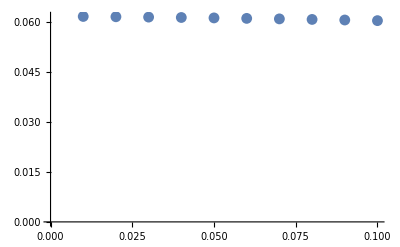

```mathematica
ListPlot[KappavsBeta,AxesOrigin->{0,0}]
```

## σ at large μ for Daniel 2015-06-19

```mathematica
NL=5;
NC=20;
NR=5;
NT=NL+NC+NR;

w=1.0;
ww=1.0;

t=200.0;
dt=0.1;

cut=10^2;

μC=0.0;
```

```mathematica
SigmavsBeta={};

For[i=1,i≤ 1,i++,
β=0.01*i;
data={};
(*j upper bound was 900*)
For[j=1,j≤ 3,j++,

μL=-20.0*j;
μR=+20.0*j;
βL = βC = βR = β;

G=Solver[NL,NC,NR,βL,βC,βR,μL,μC,μR,w,ww,t,dt,cut];
data=Append[data,{μR*β,Im[G[[NL+NC/2+1,NL+NC/2]]-G[[NL+NC/2,NL+NC/2+1]]]}];
Print[data[[j]]];
];
sigma=LinearModelFit[data,x,x]//Normal//Coefficient[#,x]&;
SigmavsBeta = Append[SigmavsBeta,{β,sigma}];
]
```

{40.,0.0484047}

{80.,0.0948025}

{120.,0.1373}

{160.,0.174226}

{200.,0.204229}

{240.,0.226372}

{280.,0.240199}

{320.,0.245787}

{360.,0.243745}

{400.,0.235138}

{440.,0.221362}

{480.,0.203954}

{520.,0.184413}

{560.,0.164056}

{600.,0.143933}

{640.,0.124803}

{680.,0.107152}

{720.,0.0912432}

{760.,0.0771672}

{800.,2.714806808601×10^977}

{840.,3.1165220834701×10^2794}

{880.,2.2278192186472×10^4609}

{920.,1.6638920949932×10^6310}

{960.,5.8282341396523×10^6312}

{1000.,5.8282341396253×10^6312}

{1040.,5.8282341396882×10^6312}

{1080.,5.8282341396982×10^6312}

{1120.,5.828234139701×10^6312}

{1160.,5.8282341396198×10^6312}

$Aborted

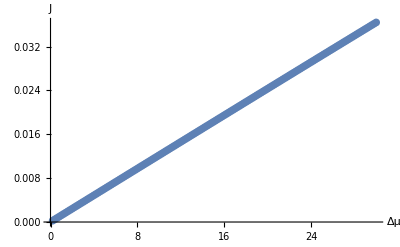

```mathematica
ListPlot[data,AxesLabel->{"Δμ","J"}]
```

```mathematica
?Save
```

Save[filename,symbol] appends definitions associated with the specified symbol to a file. 
Save[filename,form] appends definitions associated with all symbols whose names match the string pattern "form". 
Save[filename,context`] appends definitions associated with all symbols in the specified context. 
Save[filename,{object_1,object_2,…}] appends definitions associated with several objects.

```mathematica
?Put
```

expr>>filename writes expr to a file. 
Put[expr_1,expr_2,…,filename] writes a sequence of expressions expr_i to a file. 
Put[filename] creates an empty file with the specified name.

```mathematica
data>>"large_mu_sweep"
```

```mathematica
Export["large_mu",data,"CSV"]
```

large_mu

```mathematica
Directory[]
```

/Users/raghu